```mathematica
2-2
```

0

```mathematica
CompConj[A_] := A /.Complex[0,n_]->-Complex[0,n]
```

# Quantum Lissajous Motion

Nicholas Wheeler
Reed College Physics Motion
13 April 2008

### Introduction

A few days ago I received a request from the editor of the American Journal of Physics to referee a manuscript submitted by Meredith A. Mahoney, David M. Paganin & Helen M. L. Faulkner, all of whom are/were attached to the School of Physics, Monash University in Victoria, Australia. Their paper bears the title "Quantum-mechanical phase vortices in the two-dimensional infinite square well." The School of Physics maintains an elaborate web site, which, however, makes no mention of either Mahoney or Paganin, who I suspect were students of Faulkner

```mathematica
Hyperlink["Faulkner","http://www.physics.monash.edu.au/staff/faulkner.html"]
```

Faulkner lists electron microscopy, diffraction physics, phase retrieval and optical vortices as primary interests, and co-authored papers—one entitled "Phase retrieval and aberration correction in the presence of vortices in high-resolution transmission electron microscopy"—with Paganin in 2001 and 2003. I suspect she is the source of the references to "phase vortices" in the paper  (emphasized in its title), which appear to me to be entirely extraneous to the paper's small but interesting point.

Here I describe the path—the rectilinear Lissajous figure—traced by a particle that bounces around elastically in a square box. The subject is almost too simple to require discussion classically, but will be found to acquire some interest when treated quantum mechanically.

CLASSICAL THEORY

### Particle motion in a one-dimensional box

A particle bounced back and forth between the ends of a one-dimensional box of length a. The motion is periodic, with period  τ = 2a/v , where v refers to its constant speed. The situation is too simple to discuss; my challenge here is to teach Mathematica how to draw such an  x[t].

I will assume henceforth that the box is a unit box (a = 1). I assume that the particle is launched from  0 < x0 < 1 and that initially it moves to the right with speed v.  Its subsequent motion requires piecewise description, on the following pattern:

```mathematica
Piecewise[{
{x0+v t,0<t<(1-x0)/v},
{2-x0-v t,(1-x0)/v<t<(2-x0)/v},
{v t-2+x0,(2-x0)/v<t<(3-x0)/v},
{4-x0-v t,(3-x0)/v<t<(4-x0)/v},
{v t-4+x0,(4-x0)/v<t<(5-x0)/v}}]
```

Piecewise[{{t v+x0, 0<t<(1-x0)/v}, {2-t v-x0, (1-x0)/v<t<(2-x0)/v}, {-2+t v+x0, (2-x0)/v<t<(3-x0)/v}, {4-t v-x0, (3-x0)/v<t<(4-x0)/v}, {-4+t v+x0, (4-x0)/v<t<(5-x0)/v}, {0, True}}]

Here I construct a description of the motion during a longer sequence of bounces:

```mathematica
A=Table[{{2n-x0-v t,((2n-1)-x0)/v<t<(2n-x0)/v},
{v t-2n+x0,(2n-x0)/v<t<((2n+1)-x0)/v}},{n,0,50}];
```

```mathematica
Segments={Part[A,1,1],Part[A,1,2],Part[A,2,1],Part[A,2,2],
Part[A,3,1],Part[A,3,2],Part[A,4,1],Part[A,4,2],
Part[A,5,1],Part[A,5,2],Part[A,6,1],Part[A,6,2],
Part[A,7,1],Part[A,7,2],Part[A,8,1],Part[A,8,2],
Part[A,9,1],Part[A,9,2],Part[A,10,1],Part[A,10,2],
Part[A,11,1],Part[A,11,2],Part[A,12,1],Part[A,12,2],
Part[A,13,1],Part[A,13,2],Part[A,14,1],Part[A,14,2],
Part[A,15,1],Part[A,15,2],Part[A,16,1],Part[A,16,2],
Part[A,17,1],Part[A,17,2],Part[A,18,1],Part[A,18,2],
Part[A,19,1],Part[A,19,2],Part[A,20,1],Part[A,20,2],
Part[A,21,1],Part[A,21,2],Part[A,22,1],Part[A,22,2],
Part[A,23,1],Part[A,23,2],Part[A,24,1],Part[A,24,2],
Part[A,25,1],Part[A,25,2],Part[A,26,1],Part[A,26,2],
Part[A,27,1],Part[A,27,2],Part[A,28,1],Part[A,28,2],
Part[A,29,1],Part[A,29,2],Part[A,30,1],Part[A,30,2],
Part[A,31,1],Part[A,31,2],Part[A,32,1],Part[A,32,2],
Part[A,33,1],Part[A,33,2],Part[A,34,1],Part[A,34,2],
Part[A,35,1],Part[A,35,2],Part[A,36,1],Part[A,36,2],
Part[A,37,1],Part[A,37,2],Part[A,38,1],Part[A,38,2],Part[A,39,1],Part[A,39,2],Part[A,40,1],Part[A,40,2],
Part[A,41,1],Part[A,41,2],Part[A,42,1],Part[A,42,2],
Part[A,43,1],Part[A,43,2],Part[A,44,1],Part[A,44,2],
Part[A,45,1],Part[A,45,2],Part[A,46,1],Part[A,46,2],Part[A,47,1],Part[A,47,2],Part[A,48,1],Part[A,48,2],
Part[A,49,1],Part[A,49,2],Part[A,50,1],Part[A,50,2]};
```

```mathematica
x[t_]:=Piecewise[Segments]
```

we have in hand a description of the flight of the particle that can be used for times

0<t<(99-x0)/v

Assigning particular values to the speed and initial position

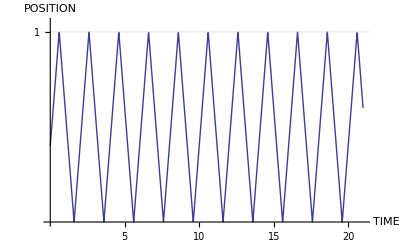

```mathematica
X[t_]:=x[t]/.{x0->0.4, v->1}
Plot[Evaluate[X[t]],{t,0,21},PlotRange->{0,1.05}, GridLines->{{},{1}}, Ticks->{{5,10,15,20},{1}}, AxesLabel->{"TIME","POSITION"}]
```

### Particle motion in a two-dimensional box

The particle bounces back and forth with period

```mathematica
Subscript[τ, x]=2/Subscript[v, x]
```

2/v_x

up and down with period

```mathematica
Subscript[τ, y]=2/Subscript[v, y]
```

2/v_y

tracing a curve which will be closed iff

```mathematica
Subscript[τ, x]/Subscript[τ, y]=Subscript[v, y]/Subscript[v, x]
```

v_y/v_x

is rational. I construct examples of such curves:

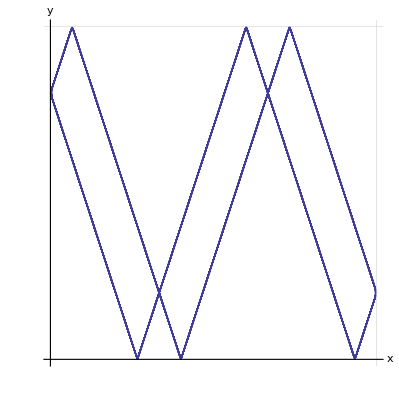

```mathematica
X[t_] := x[t] /. {x0 -> .4, v -> 1}
Y[t_] := x[t] /. {x0 -> 0, v -> 3}
ParametricPlot[Evaluate[{X[t],Y[t]}], {t,0,20},GridLines->{{1},{1}}, Ticks->False, AxesLabel->{x,y}, LabelStyle->Large]
```

Here is a slightly de-tuned variant of the preceding figure:

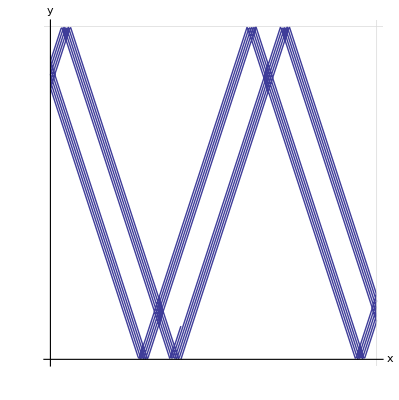

```mathematica
X[t_] := x[t] /. {x0 -> .4, v -> 1}
Y[t_] := x[t] /. {x0 -> 0, v -> 3.01}
ParametricPlot[Evaluate[{X[t],Y[t]}], {t,0,10},GridLines->{{1},{1}}, Ticks->False, AxesLabel->{x,y}, LabelStyle->Large]
```

The following commands permit one to construct unlimitedly many slightly de-tuned instances of the simplest kind of Lissajous figures—those in which right/left and up/down traversals occur with the same (or nearly the same) period:

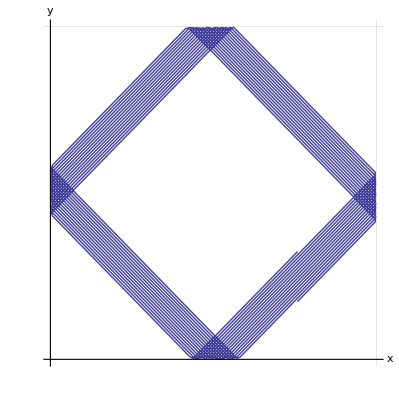

```mathematica
X[t_] := x[t] /. {x0 ->RandomReal[], v ->1}
Y[t_] := x[t] /. {x0 ->RandomReal[], v ->1.005}
ParametricPlot[Evaluate[{X[t],Y[t]}], {t,0,30},GridLines->{{1},{1}}, Ticks->False, AxesLabel->{x,y}, LabelStyle->Large]
```

QUANTUM THEORY

### Motion of probability density in a one-dimensional box

We introduce functions that are normalized on the unit interval, and vanish at the endpoints of the interval:

```mathematica
f1[x_]:=√2 Sin[1π x]
f2[x_]:=√2 Sin[2π x]
f3[x_]:=√2 Sin[3π x]
f4[x_]:=√2 Sin[4π x]
f5[x_]:=√2 Sin[5π x]
```

```mathematica
∫_0^1 f1[x]^2 ⅆx
∫_0^1 f2[x]^2 ⅆx
∫_0^1 f3[x]^2 ⅆx
```

1

1

1

```mathematica
f1[0]
f1[1]

f2[0]
f2[1]

f3[0]
f3[1]
```

0

0

0

«3 more identical outputs»

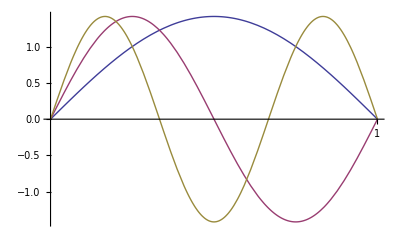

```mathematica
Plot[{f1[x],f2[x],f3[x]},{x,0,1}, Ticks->{{1},{}}]
```

We adopt units in which the Schrödinger reads

-(∂_x)^2 ψ=ⅈ∂_t ψ

and observe that these "harmonically buzzing eigenfunctions"

```mathematica
F1[x_,t_]:=f1[x]Exp[-ⅈ (1π)^2 t]
F2[x_,t_]:=f2[x]Exp[-ⅈ (2π)^2 t]
F3[x_,t_]:=f3[x]Exp[-ⅈ (3π)^2 t]
F4[x_,t_]:=f4[x]Exp[-ⅈ (4π)^2 t]
F5[x_,t_]:=f5[x]Exp[-ⅈ (5π)^2 t]
```

are indeed solutions of the Schrödinger equation:

```mathematica
-D[F1[x,t],{x,2}]==ⅈ D[F1[x,t],{t,1}]
-D[F2[x,t],{x,2}]==ⅈ D[F2[x,t],{t,1}]
-D[F3[x,t],{x,2}]==ⅈ D[F3[x,t],{t,1}]
```

True

True

True

Ther associated probabiity densities are seen to be static:

```mathematica
CompConj[F1[x,t]]F1[x,t]
CompConj[F2[x,t]]F2[x,t]
CompConj[F3[x,t]]F3[x,t]
```

2 Sin[π x]^2

2 Sin[2 π x]^2

2 Sin[3 π x]^2

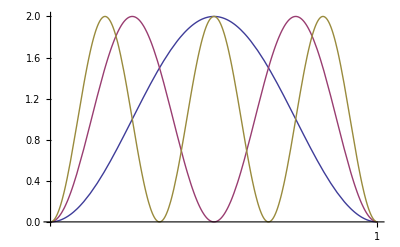

```mathematica
Plot[{2 Sin[π x]^2,2 Sin[2π x]^2,2 Sin[3π x]^2}, {x,0,1}, Ticks->{{1},{}}]
```

Sloshing motion of the probability densities of superimposed eigenstates:

Look now to this simplest-possible superposition of buzzing eigenstates

```mathematica
Ψ12[x_,t_,α_]:=Cos[α]F1[x,t]+Sin[α]F2[x,t-δ]
```

where α is a "mixing angle." We construct the associated probability density

```mathematica
CompConj[Ψ12[x,t,α]]Ψ12[x,t,α]//ComplexExpand
```

2 Cos[π^2 t]^2 Cos[α]^2 Sin[π x]^2+2 Cos[α]^2 Sin[π^2 t]^2 Sin[π x]^2+4 Cos[π^2 t] Cos[α] Cos[4 π^2 (t-δ)] Sin[π x] Sin[2 π x] Sin[α]+2 Cos[4 π^2 (t-δ)]^2 Sin[2 π x]^2 Sin[α]^2+4 Cos[α] Sin[π^2 t] Sin[π x] Sin[2 π x] Sin[α] Sin[4 π^2 (t-δ)]+2 Sin[2 π x]^2 Sin[α]^2 Sin[4 π^2 (t-δ)]^2

```mathematica
P12[x_,t_,α_]:=2 Cos[π^2 t]^2 Cos[α]^2 Sin[π x]^2+2 Cos[α]^2 Sin[π^2 t]^2 Sin[π x]^2+4 Cos[π^2 t] Cos[α] Cos[4 π^2 (t-δ)] Sin[π x] Sin[2 π x] Sin[α]+2 Cos[4 π^2 (t-δ)]^2 Sin[2 π x]^2 Sin[α]^2+4 Cos[α] Sin[π^2 t] Sin[π x] Sin[2 π x] Sin[α] Sin[4 π^2 (t-δ)]+2 Sin[2 π x]^2 Sin[α]^2 Sin[4 π^2 (t-δ)]^2
```

```mathematica
TrigReduce[P12[x,t,α]]
```

1/4 (4-2 Cos[2 π x]-2 Cos[4 π x]-Cos[2 π x-2 α]+Cos[4 π x-2 α]-Cos[2 π x+2 α]+Cos[4 π x+2 α]+Sin[π^2 t-3 π x-2 α-4 π^2 (t-δ)]-Sin[π^2 t-π x-2 α-4 π^2 (t-δ)]-Sin[π^2 t+π x-2 α-4 π^2 (t-δ)]+Sin[π^2 t+3 π x-2 α-4 π^2 (t-δ)]-Sin[π^2 t-3 π x+2 α-4 π^2 (t-δ)]+Sin[π^2 t-π x+2 α-4 π^2 (t-δ)]+Sin[π^2 t+π x+2 α-4 π^2 (t-δ)]-Sin[π^2 t+3 π x+2 α-4 π^2 (t-δ)])

REMARK: There is a reason I adopt a 2-step procedure in constructing P12[x, t, α].  Had I written

```mathematica
P12[x_,t_,α_]:=CompConj[Ψ12[x,t,α]]Ψ12[x,t,α]//ComplexExpand
```

I would have obtained a result that looks the same

```mathematica
P12[x,t,α]
```

2 Cos[π^2 t]^2 Cos[α]^2 Sin[π x]^2+2 Cos[α]^2 Sin[π^2 t]^2 Sin[π x]^2+4 Cos[π^2 t] Cos[α] Cos[4 π^2 (t-δ)] Sin[π x] Sin[2 π x] Sin[α]+2 Cos[4 π^2 (t-δ)]^2 Sin[2 π x]^2 Sin[α]^2+4 Cos[α] Sin[π^2 t] Sin[π x] Sin[2 π x] Sin[α] Sin[4 π^2 (t-δ)]+2 Sin[2 π x]^2 Sin[α]^2 Sin[4 π^2 (t-δ)]^2

```mathematica
2 Cos[π^2 t]^2 Cos[α]^2 Sin[π x]^2+2 Cos[α]^2 Sin[π^2 t]^2 Sin[π x]^2+4 Cos[π^2 t] Cos[4 π^2 t] Cos[α] Sin[π x] Sin[2 π x] Sin[α]+4 Cos[α] Sin[π^2 t] Sin[4 π^2 t] Sin[π x] Sin[2 π x] Sin[α]+2 Cos[4 π^2 t]^2 Sin[2 π x]^2 Sin[α]^2+2 Sin[4 π^2 t]^2 Sin[2 π x]^2 Sin[α]^2
```

2 Cos[π^2 t]^2 Cos[α]^2 Sin[π x]^2+2 Cos[α]^2 Sin[π^2 t]^2 Sin[π x]^2+4 Cos[π^2 t] Cos[4 π^2 t] Cos[α] Sin[π x] Sin[2 π x] Sin[α]+4 Cos[α] Sin[π^2 t] Sin[4 π^2 t] Sin[π x] Sin[2 π x] Sin[α]+2 Cos[4 π^2 t]^2 Sin[2 π x]^2 Sin[α]^2+2 Sin[4 π^2 t]^2 Sin[2 π x]^2 Sin[α]^2

but  that, when I assign value to α, acquires some "vanishing imaginary terms"

```mathematica
P12[x,t,0.5]
```

1.5403 Cos[π^2 t]^2 Sin[π x]^2+1.5403 Sin[π^2 t]^2 Sin[π x]^2+1.68294 Cos[π^2 t] Cos[4 π^2 (t-δ)] Sin[π x] Sin[2 π x]+0.459698 Cos[4 π^2 (t-δ)]^2 Sin[2 π x]^2+1.68294 Sin[π^2 t] Sin[π x] Sin[2 π x] Sin[4 π^2 (t-δ)]+0.459698 Sin[2 π x]^2 Sin[4 π^2 (t-δ)]^2+ⅈ (0. Cos[π^2 t] Sin[π^2 t] Sin[π x]^2+0. Cos[4 π^2 (t-δ)] Sin[π^2 t] Sin[π x] Sin[2 π x]+0. Cos[π^2 t] Sin[π x] Sin[2 π x] Sin[4 π^2 (t-δ)]+0. Cos[4 π^2 (t-δ)] Sin[2 π x]^2 Sin[4 π^2 (t-δ)])

```mathematica
1.54030230586814 Cos[π^2 t]^2 Sin[π x]^2+1.54030230586814 Sin[π^2 t]^2 Sin[π x]^2+1.6829419696157932 Cos[π^2 t] Cos[4 π^2 t] Sin[π x] Sin[2 π x]+1.6829419696157932 Sin[π^2 t] Sin[4 π^2 t] Sin[π x] Sin[2 π x]+0.4596976941318603 Cos[4 π^2 t]^2 Sin[2 π x]^2+0.4596976941318603 Sin[4 π^2 t]^2 Sin[2 π x]^2+ⅈ (0. Cos[π^2 t] Sin[π^2 t] Sin[π x]^2+0. Cos[4 π^2 t] Sin[π^2 t] Sin[π x] Sin[2 π x]+0. Cos[π^2 t] Sin[4 π^2 t] Sin[π x] Sin[2 π x]+0. Cos[4 π^2 t] Sin[4 π^2 t] Sin[2 π x]^2)
```

1.5403 Cos[π^2 t]^2 Sin[π x]^2+1.5403 Sin[π^2 t]^2 Sin[π x]^2+1.68294 Cos[π^2 t] Cos[4 π^2 t] Sin[π x] Sin[2 π x]+1.68294 Sin[π^2 t] Sin[4 π^2 t] Sin[π x] Sin[2 π x]+0.459698 Cos[4 π^2 t]^2 Sin[2 π x]^2+0.459698 Sin[4 π^2 t]^2 Sin[2 π x]^2+ⅈ (0. Cos[π^2 t] Sin[π^2 t] Sin[π x]^2+0. Cos[4 π^2 t] Sin[π^2 t] Sin[π x] Sin[2 π x]+0. Cos[π^2 t] Sin[4 π^2 t] Sin[π x] Sin[2 π x]+0. Cos[4 π^2 t] Sin[4 π^2 t] Sin[2 π x]^2)

the presence of which causes some commands (particularly: graphics commands) not to work (as I have learned the hard way).

and observe that we have normalization for all values of α:

```mathematica
∫_0^1 P12[x,t,α]ⅆx
```

1

Experimenting with the following adjustable figure

```mathematica
Manipulate[Plot[P12[x,0,α],{x,0,1},Ticks->{{1},{}}],{α,0,π}]
```

I am motivated by my present 2D intentions to assign to α this particular value:

```mathematica
MixingAngle12=0.527788;
```

The initial probability distribution looks then like this:

```mathematica
Plot[P12[x,0,MixingAngle12],{x,0,1},Ticks->{{1},{}}]
```

-Graphics-

From

```mathematica
TrigReduce[P12[x,t,α]]
```

1/4 (4-2 Cos[2 π x]-2 Cos[4 π x]-Cos[2 π x-2 α]+Cos[4 π x-2 α]-Cos[2 π x+2 α]+Cos[4 π x+2 α]+Sin[π^2 t-3 π x-2 α-4 π^2 (t-δ)]-Sin[π^2 t-π x-2 α-4 π^2 (t-δ)]-Sin[π^2 t+π x-2 α-4 π^2 (t-δ)]+Sin[π^2 t+3 π x-2 α-4 π^2 (t-δ)]-Sin[π^2 t-3 π x+2 α-4 π^2 (t-δ)]+Sin[π^2 t-π x+2 α-4 π^2 (t-δ)]+Sin[π^2 t+π x+2 α-4 π^2 (t-δ)]-Sin[π^2 t+3 π x+2 α-4 π^2 (t-δ)])

we see that the probability density oscillates with angular frequency

```mathematica
ω=3 π^2 =(2π)^2-(1π)^2
```

3 π^2

which means that it has period

```mathematica
τ=(2π)/(3 π^2)=2/(3π)
```

2/(3 π)

Which, of course, checks out:

```mathematica
P12[x,t+2/(3π),α]==P12[x,t,α]//Simplify
```

True

Here is an animated display of the sloshy oscillation:

```mathematica
Manipulate[Plot[P12[x,t,MixingAngle12],{x,0,1},PlotRange->{0,3.0}, Ticks->{{1},{}},PlotLabel->Style["Sloshing Probability Density", FontFamily->"Helvetica", FontSize->14] ],{t,0,(2/3)/π}]
```

The time-dependence of the probability density arose from a construction of the form

```mathematica
CompConj[a ⅇ^(-ⅈ Subscript[ω, 1] t)+b ⅇ^(-ⅈ Subscript[ω, 2] t)](a ⅇ^(-ⅈ Subscript[ω, 1] t)+b ⅇ^(-ⅈ Subscript[ω, 2] t))//ComplexExpand//Simplify
```

a^2+b^2+2 a b Cos[t ((3 π^2)_1-(3 π^2)_2)]

and lives in the cross term, demonstrating the truth of the general proposition that in the quantum world, motion is an interference effect.



We next construct the associated probability current:

```mathematica
-ⅈ(CompConj[Ψ12[x,t,α]]D[Ψ12[x,t,α],x]-Ψ12[x,t,α]D[CompConj[Ψ12[x,t,α]],x])//ComplexExpand
```

8 π Cos[2 π x] Cos[α] Cos[4 π^2 (t-δ)] Sin[π^2 t] Sin[π x] Sin[α]-4 π Cos[π x] Cos[α] Cos[4 π^2 (t-δ)] Sin[π^2 t] Sin[2 π x] Sin[α]-8 π Cos[π^2 t] Cos[2 π x] Cos[α] Sin[π x] Sin[α] Sin[4 π^2 (t-δ)]+4 π Cos[π^2 t] Cos[π x] Cos[α] Sin[2 π x] Sin[α] Sin[4 π^2 (t-δ)]

```mathematica
J12[x_,t_,α_]:=8 π Cos[4 π^2 t] Cos[2 π x] Cos[α] Sin[π^2 t] Sin[π x] Sin[α]-8 π Cos[π^2 t] Cos[2 π x] Cos[α] Sin[4 π^2 t] Sin[π x] Sin[α]-4 π Cos[4 π^2 t] Cos[π x] Cos[α] Sin[π^2 t] Sin[2 π x] Sin[α]+4 π Cos[π^2 t] Cos[π x] Cos[α] Sin[4 π^2 t] Sin[2 π x] Sin[α]
```

Generally, one expects to have

```mathematica
D[P, t]+∇•J=0
```

0

which in the present one-dimensional context reads

```mathematica
D[P12[x,t,α],t]+D[J12[x,t,α],x]==0
```

-12 π^2 Cos[4 π^2 t] Cos[α] Sin[π^2 t] Sin[π x] Sin[2 π x] Sin[α]+12 π^2 Cos[α] Cos[4 π^2 (t-δ)] Sin[π^2 t] Sin[π x] Sin[2 π x] Sin[α]+12 π^2 Cos[π^2 t] Cos[α] Sin[4 π^2 t] Sin[π x] Sin[2 π x] Sin[α]-12 π^2 Cos[π^2 t] Cos[α] Sin[π x] Sin[2 π x] Sin[α] Sin[4 π^2 (t-δ)]==0

Here I superimpose representations of the moving probability density and moving current:

```mathematica
Manipulate[Plot[{P12[x,t,MixingAngle12],J12[x,t,MixingAngle12]},{x,0,1}, Ticks->{{1},{}},PlotRange->{-15,15},PlotLabel->Style["Moving Probability Density & Current", FontFamily->"Helvetica", FontSize->14]],{t,0,(2/3)/π} ]
```

Construction of an alternative pair of superimposed states:

A state that better serves needs that will arise when—which is our primary objective—we look to quantum physics in two-dimensional boxes is the state

```mathematica
Ψ13[x_,t_,α_]:=Cos[α]F1[x,t]+Sin[α]F3[x,t]
```

From

```mathematica
CompConj[Ψ13[x, t, α]] Ψ13[x, t, α] // ComplexExpand
```

2 Cos[π^2 t]^2 Cos[α]^2 Sin[π x]^2+2 Cos[α]^2 Sin[π^2 t]^2 Sin[π x]^2+4 Cos[π^2 t] Cos[9 π^2 t] Cos[α] Sin[π x] Sin[3 π x] Sin[α]+4 Cos[α] Sin[π^2 t] Sin[9 π^2 t] Sin[π x] Sin[3 π x] Sin[α]+2 Cos[9 π^2 t]^2 Sin[3 π x]^2 Sin[α]^2+2 Sin[9 π^2 t]^2 Sin[3 π x]^2 Sin[α]^2

we are led to define

```mathematica
P13[x_,t_,α_]:=2 Cos[π^2 t]^2 Cos[α]^2 Sin[π x]^2+2 Cos[α]^2 Sin[π^2 t]^2 Sin[π x]^2+4 Cos[π^2 t] Cos[9 π^2 t] Cos[α] Sin[π x] Sin[3 π x] Sin[α]+4 Cos[α] Sin[π^2 t] Sin[9 π^2 t] Sin[π x] Sin[3 π x] Sin[α]+2 Cos[9 π^2 t]^2 Sin[3 π x]^2 Sin[α]^2+2 Sin[9 π^2 t]^2 Sin[3 π x]^2 Sin[α]^2
```

which is seen by

```mathematica
TrigReduce[P13[x,t,α]]
```

1/4 (4-2 Cos[2 π x]-2 Cos[6 π x]-Cos[2 π x-2 α]+Cos[6 π x-2 α]-Cos[2 π x+2 α]+Cos[6 π x+2 α]+Sin[8 π^2 t-4 π x-2 α]-Sin[8 π^2 t-2 π x-2 α]-Sin[8 π^2 t+2 π x-2 α]+Sin[8 π^2 t+4 π x-2 α]-Sin[8 π^2 t-4 π x+2 α]+Sin[8 π^2 t-2 π x+2 α]+Sin[8 π^2 t+2 π x+2 α]-Sin[8 π^2 t+4 π x+2 α])

to oscillate with period

```mathematica
τ=1/(4π)
```

1/(4 π)

The persistent bilateral symmetry of the figures displayed below

```mathematica
Manipulate[Plot[P13[x,0,α],{x,0,1}],{α,0,π}]
```

recommends no particular α-value to our attention. I semi-arbitrarily set

```mathematica
MixingAngle13=1.31633;
```

which leads to an initial probability density of the form

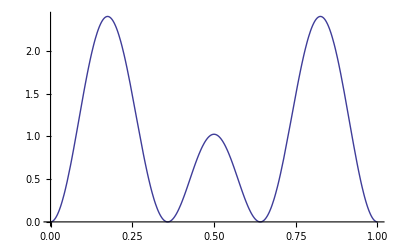

```mathematica
Plot[P13[x,0,MixingAngle13],{x,0,1}]
```

Had we retained our old mixing angle we would have obtained

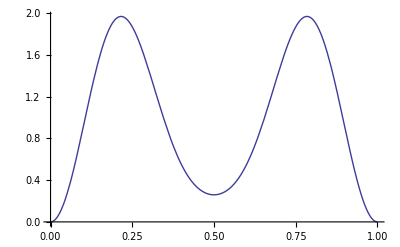

```mathematica
Plot[P13[x,0,MixingAngle12],{x,0,1}]
```

### Lissajous motion of probability density in a two-dimensional box

We are in position at last to consider quantum mechanical analogs of the classical rectilinear Lissajous figures discussed previously. This turns out to be a subject with a literature

```mathematica
Hyperlink["Quantum mechanical Lissajous figures", "http://www.google.com/search?hl=en&q=quantum+mechanical+Lissajous&btnG=Search" ]
```

Much of this work has to do with semi-classical quantum mechanics (the area where classical and quantum mechanics meet), with is a subject that is still being quite actively pursued, and which has generated a vast literature with deep ramifications: see

```mathematica
Hyperlink["Large semi-classical bibliography","http://www.citebase.org/abstract?identifier=oai%3AarXiv.org%3Aquant-ph%2F0611062&action=citeshits&citeshits=cites"]
```

To expose the points at issue it is sufficient to examine an illustrative case. Use the material now in hand to construct the x,y-separated product state

```mathematica
Ψ[x_, y_, t_, α_, β_, δ_] :=Ψ13[x,t,α]Ψ13[y,t+δ,β]
```

$Failed

Dispite the simplicity of that construction, the resulting expressions for probability density and probability current become much too lengthy to permit exploration of this subject with pen and ink on paper. Animated graphics provide the only comprehending the meaning of the results to which we will be led. Those two circumstances probably explain why the subject is not treated in any of the standard textbooks.

Before proceeding further, we verify that the function thus defined is indeed a solution of the Schrödinger equation:

```mathematica
-D[Ψ[x, y, t, α, β, δ],{x,2}]-D[Ψ[x, y, t, α, β, δ],{y,2}]==ⅈ D[Ψ[x, y, t, α, β, δ],{t,1}]//Simplify
```

(-4/3 ⅇ^(-5 ⅈ π^2 t) π^2 (8 Cos[π x]+(1+2 ⅈ) Cos[π y]) Sin[π x] Sin[π y])[x,y,t,α,β,δ]+(-8/3 ⅇ^(-5 ⅈ π^2 t) π^2 (Cos[π x]+(2+4 ⅈ) Cos[π y]) Sin[π x] Sin[π y])[x,y,t,α,β,δ]+ⅈ ((-20/3 ⅈ ⅇ^(-5 ⅈ π^2 t) π^2 (2 Cos[π x]+(1+2 ⅈ) Cos[π y]) Sin[π x] Sin[π y])[x,y,t,α,β,δ]+(4/3 ⅇ^(-5 ⅈ π^2 t) (2 Cos[π x]+(1+2 ⅈ) Cos[π y]) Sin[π x] Sin[π y])^(0,0,1,0,0,0)[x,y,t,α,β,δ])+(4/3 ⅇ^(-5 ⅈ π^2 t) π ((1+2 ⅈ) Cos[2 π y] Sin[π x]+Cos[π y] Sin[2 π x]))^(0,1,0,0,0,0)[x,y,t,α,β,δ]+(4/3 ⅇ^(-5 ⅈ π^2 t) (2 Cos[π x]+(1+2 ⅈ) Cos[π y]) Sin[π x] Sin[π y])^(0,2,0,0,0,0)[x,y,t,α,β,δ]+(2/3 ⅇ^(-5 ⅈ π^2 t) π (4 Cos[2 π x] Sin[π y]+(1+2 ⅈ) Cos[π x] Sin[2 π y]))^(1,0,0,0,0,0)[x,y,t,α,β,δ]+(4/3 ⅇ^(-5 ⅈ π^2 t) (2 Cos[π x]+(1+2 ⅈ) Cos[π y]) Sin[π x] Sin[π y])^(2,0,0,0,0,0)[x,y,t,α,β,δ]+(4/3 ⅇ^(-5 ⅈ π^2 t) π ((1+2 ⅈ) Cos[2 π y] Sin[π x]+Cos[π y] Sin[2 π x]) Derivative[0,1,0,0,0,0]'[4/3 ⅇ^(-5 ⅈ π^2 t) (2 Cos[π x]+(1+2 ⅈ) Cos[π y]) Sin[π x] Sin[π y]])[x,y,t,α,β,δ]+(2/3 ⅇ^(-5 ⅈ π^2 t) π (4 Cos[2 π x] Sin[π y]+(1+2 ⅈ) Cos[π x] Sin[2 π y]) Derivative[1,0,0,0,0,0]'[4/3 ⅇ^(-5 ⅈ π^2 t) (2 Cos[π x]+(1+2 ⅈ) Cos[π y]) Sin[π x] Sin[π y]])[x,y,t,α,β,δ]==0

Turn now to the construction of the probability density:

```mathematica
CompConj[Ψ[x,y,t,α,β,δ]]Ψ[x,y,t,α,β,δ]//ComplexExpand
```

-Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Im[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]+Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]+ⅈ (Im[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]+Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]])

```mathematica
Length[%]
```

3

```mathematica
P[x_,y_,t_,α_,β_,δ_]:=4 Cos[π^2 t]^2 Cos[α]^2 Cos[β]^2 Cos[π^2 (t+δ)]^2 Sin[π x]^2 Sin[π y]^2+4 Cos[α]^2 Cos[β]^2 Cos[π^2 (t+δ)]^2 Sin[π^2 t]^2 Sin[π x]^2 Sin[π y]^2+8 Cos[π^2 t] Cos[9 π^2 t] Cos[α] Cos[β]^2 Cos[π^2 (t+δ)]^2 Sin[π x] Sin[3 π x] Sin[π y]^2 Sin[α]+8 Cos[α] Cos[β]^2 Cos[π^2 (t+δ)]^2 Sin[π^2 t] Sin[9 π^2 t] Sin[π x] Sin[3 π x] Sin[π y]^2 Sin[α]+4 Cos[9 π^2 t]^2 Cos[β]^2 Cos[π^2 (t+δ)]^2 Sin[3 π x]^2 Sin[π y]^2 Sin[α]^2+4 Cos[β]^2 Cos[π^2 (t+δ)]^2 Sin[9 π^2 t]^2 Sin[3 π x]^2 Sin[π y]^2 Sin[α]^2+8 Cos[π^2 t]^2 Cos[α]^2 Cos[β] Cos[π^2 (t+δ)] Cos[9 π^2 (t+δ)] Sin[π x]^2 Sin[π y] Sin[3 π y] Sin[β]+8 Cos[α]^2 Cos[β] Cos[π^2 (t+δ)] Cos[9 π^2 (t+δ)] Sin[π^2 t]^2 Sin[π x]^2 Sin[π y] Sin[3 π y] Sin[β]+16 Cos[π^2 t] Cos[9 π^2 t] Cos[α] Cos[β] Cos[π^2 (t+δ)] Cos[9 π^2 (t+δ)] Sin[π x] Sin[3 π x] Sin[π y] Sin[3 π y] Sin[α] Sin[β]+16 Cos[α] Cos[β] Cos[π^2 (t+δ)] Cos[9 π^2 (t+δ)] Sin[π^2 t] Sin[9 π^2 t] Sin[π x] Sin[3 π x] Sin[π y] Sin[3 π y] Sin[α] Sin[β]+8 Cos[9 π^2 t]^2 Cos[β] Cos[π^2 (t+δ)] Cos[9 π^2 (t+δ)] Sin[3 π x]^2 Sin[π y] Sin[3 π y] Sin[α]^2 Sin[β]+8 Cos[β] Cos[π^2 (t+δ)] Cos[9 π^2 (t+δ)] Sin[9 π^2 t]^2 Sin[3 π x]^2 Sin[π y] Sin[3 π y] Sin[α]^2 Sin[β]+4 Cos[π^2 t]^2 Cos[α]^2 Cos[9 π^2 (t+δ)]^2 Sin[π x]^2 Sin[3 π y]^2 Sin[β]^2+4 Cos[α]^2 Cos[9 π^2 (t+δ)]^2 Sin[π^2 t]^2 Sin[π x]^2 Sin[3 π y]^2 Sin[β]^2+8 Cos[π^2 t] Cos[9 π^2 t] Cos[α] Cos[9 π^2 (t+δ)]^2 Sin[π x] Sin[3 π x] Sin[3 π y]^2 Sin[α] Sin[β]^2+8 Cos[α] Cos[9 π^2 (t+δ)]^2 Sin[π^2 t] Sin[9 π^2 t] Sin[π x] Sin[3 π x] Sin[3 π y]^2 Sin[α] Sin[β]^2+4 Cos[9 π^2 t]^2 Cos[9 π^2 (t+δ)]^2 Sin[3 π x]^2 Sin[3 π y]^2 Sin[α]^2 Sin[β]^2+4 Cos[9 π^2 (t+δ)]^2 Sin[9 π^2 t]^2 Sin[3 π x]^2 Sin[3 π y]^2 Sin[α]^2 Sin[β]^2+4 Cos[π^2 t]^2 Cos[α]^2 Cos[β]^2 Sin[π x]^2 Sin[π y]^2 Sin[π^2 (t+δ)]^2+4 Cos[α]^2 Cos[β]^2 Sin[π^2 t]^2 Sin[π x]^2 Sin[π y]^2 Sin[π^2 (t+δ)]^2+8 Cos[π^2 t] Cos[9 π^2 t] Cos[α] Cos[β]^2 Sin[π x] Sin[3 π x] Sin[π y]^2 Sin[α] Sin[π^2 (t+δ)]^2+8 Cos[α] Cos[β]^2 Sin[π^2 t] Sin[9 π^2 t] Sin[π x] Sin[3 π x] Sin[π y]^2 Sin[α] Sin[π^2 (t+δ)]^2+4 Cos[9 π^2 t]^2 Cos[β]^2 Sin[3 π x]^2 Sin[π y]^2 Sin[α]^2 Sin[π^2 (t+δ)]^2+4 Cos[β]^2 Sin[9 π^2 t]^2 Sin[3 π x]^2 Sin[π y]^2 Sin[α]^2 Sin[π^2 (t+δ)]^2+8 Cos[π^2 t]^2 Cos[α]^2 Cos[β] Sin[π x]^2 Sin[π y] Sin[3 π y] Sin[β] Sin[π^2 (t+δ)] Sin[9 π^2 (t+δ)]+8 Cos[α]^2 Cos[β] Sin[π^2 t]^2 Sin[π x]^2 Sin[π y] Sin[3 π y] Sin[β] Sin[π^2 (t+δ)] Sin[9 π^2 (t+δ)]+16 Cos[π^2 t] Cos[9 π^2 t] Cos[α] Cos[β] Sin[π x] Sin[3 π x] Sin[π y] Sin[3 π y] Sin[α] Sin[β] Sin[π^2 (t+δ)] Sin[9 π^2 (t+δ)]+16 Cos[α] Cos[β] Sin[π^2 t] Sin[9 π^2 t] Sin[π x] Sin[3 π x] Sin[π y] Sin[3 π y] Sin[α] Sin[β] Sin[π^2 (t+δ)] Sin[9 π^2 (t+δ)]+8 Cos[9 π^2 t]^2 Cos[β] Sin[3 π x]^2 Sin[π y] Sin[3 π y] Sin[α]^2 Sin[β] Sin[π^2 (t+δ)] Sin[9 π^2 (t+δ)]+8 Cos[β] Sin[9 π^2 t]^2 Sin[3 π x]^2 Sin[π y] Sin[3 π y] Sin[α]^2 Sin[β] Sin[π^2 (t+δ)] Sin[9 π^2 (t+δ)]+4 Cos[π^2 t]^2 Cos[α]^2 Sin[π x]^2 Sin[3 π y]^2 Sin[β]^2 Sin[9 π^2 (t+δ)]^2+4 Cos[α]^2 Sin[π^2 t]^2 Sin[π x]^2 Sin[3 π y]^2 Sin[β]^2 Sin[9 π^2 (t+δ)]^2+8 Cos[π^2 t] Cos[9 π^2 t] Cos[α] Sin[π x] Sin[3 π x] Sin[3 π y]^2 Sin[α] Sin[β]^2 Sin[9 π^2 (t+δ)]^2+8 Cos[α] Sin[π^2 t] Sin[9 π^2 t] Sin[π x] Sin[3 π x] Sin[3 π y]^2 Sin[α] Sin[β]^2 Sin[9 π^2 (t+δ)]^2+4 Cos[9 π^2 t]^2 Sin[3 π x]^2 Sin[3 π y]^2 Sin[α]^2 Sin[β]^2 Sin[9 π^2 (t+δ)]^2+4 Sin[9 π^2 t]^2 Sin[3 π x]^2 Sin[3 π y]^2 Sin[α]^2 Sin[β]^2 Sin[9 π^2 (t+δ)]^2
```

The command

```mathematica
TrigReduce[P[x,y,t,α,β,δ]];
```

produces a sum of

```mathematica
Length[%]
```

421

terms, of which the final term  1/32 Sin[6 π x+4 π y+2 α+2 β+8 π^2 (t+δ)]is entirely typical, and shows that P[x, y, t, α, β, δ] oscillates with period

```mathematica
τ=1/(4π)
```

1/(4 π)

We are gratified to be assured that (by a calculation that takes Mathematica the better part of a minute)

```mathematica
∫_0^1 (∫_0^1 P[x,y,t,α,β,δ]ⅆx)ⅆy//Timing
```

{67.3457,1}

In the following figures I have (by setting δ = -τ/4) arranged for the y-motion to lag the x-motion by π/2 radians.  Both figures correspond, therefore, to this classical motion

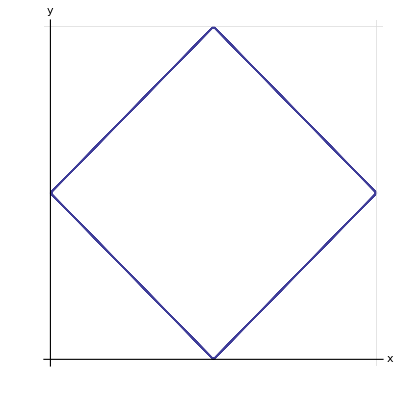

```mathematica
X[t_] := x[t] /. {x0 -> .5, v -> 1}
Y[t_] := x[t] /. {x0 -> 0, v -> 1}
ParametricPlot[Evaluate[{X[t],Y[t]}], {t,0,20},GridLines->{{1},{1}}, Ticks->False, AxesLabel->{x,y}, LabelStyle->Large]
```

Here are two alternative displays of the shifting shape and motion of the probabiity density:

```mathematica
Manipulate[ContourPlot[Evaluate[P[x,y,1/(4π)n/12,MixingAngle13,MixingAngle13,-1/(16π)]],{x,0,1},{y,0,1}],{n,0,11}]
```

```mathematica
Manipulate[Plot3D[Evaluate[P[x,y,1/(4π)n/12,MixingAngle13,MixingAngle13,-1/(16π)]],{x,0,1},{y,0,1}],{n,0,11}]
```

Compare those with the figures that result if we elect to retain our former mixing angle:

```mathematica
Manipulate[ContourPlot[Evaluate[P[x,y,1/(4π)n/12,MixingAngle12,MixingAngle12,-1/(16π)]],{x,0,1},{y,0,1}],{n,0,11}]
```

```mathematica
Manipulate[Plot3D[Evaluate[P[x,y,1/(4π)n/12,MixingAngle12,MixingAngle12,-1/(16π)]],{x,0,1},{y,0,1}],{n,0,11}]
```

### Probability current

We look next to the probability current, which has acquired now the character of a 2-vector. We look first to the x-component

```mathematica
-ⅈ(CompConj[Ψ[x, y, t, α, β, δ]]D[Ψ[x, y, t, α, β, δ],x]-Ψ[x, y, t, α, β, δ]D[CompConj[Ψ[x, y, t, α, β, δ]],x])//ComplexExpand
```

Im[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(8/3 ⅇ^(-5 ⅈ π^2 t) π Cos[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) π Cos[π x] Sin[2 π y])[x,y,t,α,β,δ]]-Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(8/3 ⅇ^(5 ⅈ π^2 t) π Cos[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) π Cos[π x] Sin[2 π y])[x,y,t,α,β,δ]]-Im[(8/3 ⅇ^(5 ⅈ π^2 t) π Cos[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) π Cos[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]-Im[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(1,0,0,0,0,0)[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]+Im[(8/3 ⅇ^(-5 ⅈ π^2 t) π Cos[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) π Cos[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]+Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(1,0,0,0,0,0)[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]+Im[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(1,0,0,0,0,0)[x,y,t,α,β,δ]]-Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(1,0,0,0,0,0)[x,y,t,α,β,δ]]+ⅈ (-Im[(8/3 ⅇ^(5 ⅈ π^2 t) π Cos[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) π Cos[π x] Sin[2 π y])[x,y,t,α,β,δ]] Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]+Im[(8/3 ⅇ^(-5 ⅈ π^2 t) π Cos[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) π Cos[π x] Sin[2 π y])[x,y,t,α,β,δ]] Im[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]+Im[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(1,0,0,0,0,0)[x,y,t,α,β,δ]]-Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Im[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(1,0,0,0,0,0)[x,y,t,α,β,δ]]+Re[(8/3 ⅇ^(5 ⅈ π^2 t) π Cos[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) π Cos[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]-Re[(8/3 ⅇ^(-5 ⅈ π^2 t) π Cos[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) π Cos[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]-Re[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(1,0,0,0,0,0)[x,y,t,α,β,δ]]+Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(1,0,0,0,0,0)[x,y,t,α,β,δ]])

```mathematica
JX[x_, y_, t_, α_, β_, δ_]:=24 π Cos[9 π^2 t] Cos[3 π x] Cos[α] Cos[β]^2 Cos[π^2 (t+δ)]^2 Sin[π^2 t] Sin[π x] Sin[π y]^2 Sin[α]-24 π Cos[π^2 t] Cos[3 π x] Cos[α] Cos[β]^2 Cos[π^2 (t+δ)]^2 Sin[9 π^2 t] Sin[π x] Sin[π y]^2 Sin[α]-8 π Cos[9 π^2 t] Cos[π x] Cos[α] Cos[β]^2 Cos[π^2 (t+δ)]^2 Sin[π^2 t] Sin[3 π x] Sin[π y]^2 Sin[α]+8 π Cos[π^2 t] Cos[π x] Cos[α] Cos[β]^2 Cos[π^2 (t+δ)]^2 Sin[9 π^2 t] Sin[3 π x] Sin[π y]^2 Sin[α]+48 π Cos[9 π^2 t] Cos[3 π x] Cos[α] Cos[β] Cos[π^2 (t+δ)] Cos[9 π^2 (t+δ)] Sin[π^2 t] Sin[π x] Sin[π y] Sin[3 π y] Sin[α] Sin[β]-48 π Cos[π^2 t] Cos[3 π x] Cos[α] Cos[β] Cos[π^2 (t+δ)] Cos[9 π^2 (t+δ)] Sin[9 π^2 t] Sin[π x] Sin[π y] Sin[3 π y] Sin[α] Sin[β]-16 π Cos[9 π^2 t] Cos[π x] Cos[α] Cos[β] Cos[π^2 (t+δ)] Cos[9 π^2 (t+δ)] Sin[π^2 t] Sin[3 π x] Sin[π y] Sin[3 π y] Sin[α] Sin[β]+16 π Cos[π^2 t] Cos[π x] Cos[α] Cos[β] Cos[π^2 (t+δ)] Cos[9 π^2 (t+δ)] Sin[9 π^2 t] Sin[3 π x] Sin[π y] Sin[3 π y] Sin[α] Sin[β]+24 π Cos[9 π^2 t] Cos[3 π x] Cos[α] Cos[9 π^2 (t+δ)]^2 Sin[π^2 t] Sin[π x] Sin[3 π y]^2 Sin[α] Sin[β]^2-24 π Cos[π^2 t] Cos[3 π x] Cos[α] Cos[9 π^2 (t+δ)]^2 Sin[9 π^2 t] Sin[π x] Sin[3 π y]^2 Sin[α] Sin[β]^2-8 π Cos[9 π^2 t] Cos[π x] Cos[α] Cos[9 π^2 (t+δ)]^2 Sin[π^2 t] Sin[3 π x] Sin[3 π y]^2 Sin[α] Sin[β]^2+8 π Cos[π^2 t] Cos[π x] Cos[α] Cos[9 π^2 (t+δ)]^2 Sin[9 π^2 t] Sin[3 π x] Sin[3 π y]^2 Sin[α] Sin[β]^2+24 π Cos[9 π^2 t] Cos[3 π x] Cos[α] Cos[β]^2 Sin[π^2 t] Sin[π x] Sin[π y]^2 Sin[α] Sin[π^2 (t+δ)]^2-24 π Cos[π^2 t] Cos[3 π x] Cos[α] Cos[β]^2 Sin[9 π^2 t] Sin[π x] Sin[π y]^2 Sin[α] Sin[π^2 (t+δ)]^2-8 π Cos[9 π^2 t] Cos[π x] Cos[α] Cos[β]^2 Sin[π^2 t] Sin[3 π x] Sin[π y]^2 Sin[α] Sin[π^2 (t+δ)]^2+8 π Cos[π^2 t] Cos[π x] Cos[α] Cos[β]^2 Sin[9 π^2 t] Sin[3 π x] Sin[π y]^2 Sin[α] Sin[π^2 (t+δ)]^2+48 π Cos[9 π^2 t] Cos[3 π x] Cos[α] Cos[β] Sin[π^2 t] Sin[π x] Sin[π y] Sin[3 π y] Sin[α] Sin[β] Sin[π^2 (t+δ)] Sin[9 π^2 (t+δ)]-48 π Cos[π^2 t] Cos[3 π x] Cos[α] Cos[β] Sin[9 π^2 t] Sin[π x] Sin[π y] Sin[3 π y] Sin[α] Sin[β] Sin[π^2 (t+δ)] Sin[9 π^2 (t+δ)]-16 π Cos[9 π^2 t] Cos[π x] Cos[α] Cos[β] Sin[π^2 t] Sin[3 π x] Sin[π y] Sin[3 π y] Sin[α] Sin[β] Sin[π^2 (t+δ)] Sin[9 π^2 (t+δ)]+16 π Cos[π^2 t] Cos[π x] Cos[α] Cos[β] Sin[9 π^2 t] Sin[3 π x] Sin[π y] Sin[3 π y] Sin[α] Sin[β] Sin[π^2 (t+δ)] Sin[9 π^2 (t+δ)]+24 π Cos[9 π^2 t] Cos[3 π x] Cos[α] Sin[π^2 t] Sin[π x] Sin[3 π y]^2 Sin[α] Sin[β]^2 Sin[9 π^2 (t+δ)]^2-24 π Cos[π^2 t] Cos[3 π x] Cos[α] Sin[9 π^2 t] Sin[π x] Sin[3 π y]^2 Sin[α] Sin[β]^2 Sin[9 π^2 (t+δ)]^2-8 π Cos[9 π^2 t] Cos[π x] Cos[α] Sin[π^2 t] Sin[3 π x] Sin[3 π y]^2 Sin[α] Sin[β]^2 Sin[9 π^2 (t+δ)]^2+8 π Cos[π^2 t] Cos[π x] Cos[α] Sin[9 π^2 t] Sin[3 π x] Sin[3 π y]^2 Sin[α] Sin[β]^2 Sin[9 π^2 (t+δ)]^2
```

and now to the y-component:

```mathematica
-ⅈ(CompConj[Ψ[x, y, t, α, β, δ]]D[Ψ[x, y, t, α, β, δ],y]-Ψ[x, y, t, α, β, δ]D[CompConj[Ψ[x, y, t, α, β, δ]],y])//ComplexExpand
```

Im[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[((4/3+(8 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) π Cos[2 π y] Sin[π x]+4/3 ⅇ^(-5 ⅈ π^2 t) π Cos[π y] Sin[2 π x])[x,y,t,α,β,δ]]-Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[((4/3+(8 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) π Cos[2 π y] Sin[π x]+4/3 ⅇ^(5 ⅈ π^2 t) π Cos[π y] Sin[2 π x])[x,y,t,α,β,δ]]-Im[((4/3+(8 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) π Cos[2 π y] Sin[π x]+4/3 ⅇ^(5 ⅈ π^2 t) π Cos[π y] Sin[2 π x])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]-Im[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(0,1,0,0,0,0)[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]+Im[((4/3+(8 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) π Cos[2 π y] Sin[π x]+4/3 ⅇ^(-5 ⅈ π^2 t) π Cos[π y] Sin[2 π x])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]+Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(0,1,0,0,0,0)[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]+Im[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(0,1,0,0,0,0)[x,y,t,α,β,δ]]-Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(0,1,0,0,0,0)[x,y,t,α,β,δ]]+ⅈ (-Im[((4/3+(8 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) π Cos[2 π y] Sin[π x]+4/3 ⅇ^(5 ⅈ π^2 t) π Cos[π y] Sin[2 π x])[x,y,t,α,β,δ]] Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]+Im[((4/3+(8 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) π Cos[2 π y] Sin[π x]+4/3 ⅇ^(-5 ⅈ π^2 t) π Cos[π y] Sin[2 π x])[x,y,t,α,β,δ]] Im[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]+Im[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(0,1,0,0,0,0)[x,y,t,α,β,δ]]-Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Im[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(0,1,0,0,0,0)[x,y,t,α,β,δ]]+Re[((4/3+(8 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) π Cos[2 π y] Sin[π x]+4/3 ⅇ^(5 ⅈ π^2 t) π Cos[π y] Sin[2 π x])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]-Re[((4/3+(8 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) π Cos[2 π y] Sin[π x]+4/3 ⅇ^(-5 ⅈ π^2 t) π Cos[π y] Sin[2 π x])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]]-Re[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(0,1,0,0,0,0)[x,y,t,α,β,δ]]+Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,α,β,δ]] Re[(4/3 ⅇ^(5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(5 ⅈ π^2 t) Sin[π x] Sin[2 π y])^(0,1,0,0,0,0)[x,y,t,α,β,δ]])

```mathematica
JY[x_, y_, t_, α_, β_, δ_]:=24 π Cos[π^2 t]^2 Cos[3 π y] Cos[α]^2 Cos[β] Cos[9 π^2 (t+δ)] Sin[π x]^2 Sin[π y] Sin[β] Sin[π^2 (t+δ)]+24 π Cos[3 π y] Cos[α]^2 Cos[β] Cos[9 π^2 (t+δ)] Sin[π^2 t]^2 Sin[π x]^2 Sin[π y] Sin[β] Sin[π^2 (t+δ)]-8 π Cos[π^2 t]^2 Cos[π y] Cos[α]^2 Cos[β] Cos[9 π^2 (t+δ)] Sin[π x]^2 Sin[3 π y] Sin[β] Sin[π^2 (t+δ)]-8 π Cos[π y] Cos[α]^2 Cos[β] Cos[9 π^2 (t+δ)] Sin[π^2 t]^2 Sin[π x]^2 Sin[3 π y] Sin[β] Sin[π^2 (t+δ)]+48 π Cos[π^2 t] Cos[9 π^2 t] Cos[3 π y] Cos[α] Cos[β] Cos[9 π^2 (t+δ)] Sin[π x] Sin[3 π x] Sin[π y] Sin[α] Sin[β] Sin[π^2 (t+δ)]+48 π Cos[3 π y] Cos[α] Cos[β] Cos[9 π^2 (t+δ)] Sin[π^2 t] Sin[9 π^2 t] Sin[π x] Sin[3 π x] Sin[π y] Sin[α] Sin[β] Sin[π^2 (t+δ)]-16 π Cos[π^2 t] Cos[9 π^2 t] Cos[π y] Cos[α] Cos[β] Cos[9 π^2 (t+δ)] Sin[π x] Sin[3 π x] Sin[3 π y] Sin[α] Sin[β] Sin[π^2 (t+δ)]-16 π Cos[π y] Cos[α] Cos[β] Cos[9 π^2 (t+δ)] Sin[π^2 t] Sin[9 π^2 t] Sin[π x] Sin[3 π x] Sin[3 π y] Sin[α] Sin[β] Sin[π^2 (t+δ)]+24 π Cos[9 π^2 t]^2 Cos[3 π y] Cos[β] Cos[9 π^2 (t+δ)] Sin[3 π x]^2 Sin[π y] Sin[α]^2 Sin[β] Sin[π^2 (t+δ)]+24 π Cos[3 π y] Cos[β] Cos[9 π^2 (t+δ)] Sin[9 π^2 t]^2 Sin[3 π x]^2 Sin[π y] Sin[α]^2 Sin[β] Sin[π^2 (t+δ)]-8 π Cos[9 π^2 t]^2 Cos[π y] Cos[β] Cos[9 π^2 (t+δ)] Sin[3 π x]^2 Sin[3 π y] Sin[α]^2 Sin[β] Sin[π^2 (t+δ)]-8 π Cos[π y] Cos[β] Cos[9 π^2 (t+δ)] Sin[9 π^2 t]^2 Sin[3 π x]^2 Sin[3 π y] Sin[α]^2 Sin[β] Sin[π^2 (t+δ)]-24 π Cos[π^2 t]^2 Cos[3 π y] Cos[α]^2 Cos[β] Cos[π^2 (t+δ)] Sin[π x]^2 Sin[π y] Sin[β] Sin[9 π^2 (t+δ)]-24 π Cos[3 π y] Cos[α]^2 Cos[β] Cos[π^2 (t+δ)] Sin[π^2 t]^2 Sin[π x]^2 Sin[π y] Sin[β] Sin[9 π^2 (t+δ)]+8 π Cos[π^2 t]^2 Cos[π y] Cos[α]^2 Cos[β] Cos[π^2 (t+δ)] Sin[π x]^2 Sin[3 π y] Sin[β] Sin[9 π^2 (t+δ)]+8 π Cos[π y] Cos[α]^2 Cos[β] Cos[π^2 (t+δ)] Sin[π^2 t]^2 Sin[π x]^2 Sin[3 π y] Sin[β] Sin[9 π^2 (t+δ)]-48 π Cos[π^2 t] Cos[9 π^2 t] Cos[3 π y] Cos[α] Cos[β] Cos[π^2 (t+δ)] Sin[π x] Sin[3 π x] Sin[π y] Sin[α] Sin[β] Sin[9 π^2 (t+δ)]-48 π Cos[3 π y] Cos[α] Cos[β] Cos[π^2 (t+δ)] Sin[π^2 t] Sin[9 π^2 t] Sin[π x] Sin[3 π x] Sin[π y] Sin[α] Sin[β] Sin[9 π^2 (t+δ)]+16 π Cos[π^2 t] Cos[9 π^2 t] Cos[π y] Cos[α] Cos[β] Cos[π^2 (t+δ)] Sin[π x] Sin[3 π x] Sin[3 π y] Sin[α] Sin[β] Sin[9 π^2 (t+δ)]+16 π Cos[π y] Cos[α] Cos[β] Cos[π^2 (t+δ)] Sin[π^2 t] Sin[9 π^2 t] Sin[π x] Sin[3 π x] Sin[3 π y] Sin[α] Sin[β] Sin[9 π^2 (t+δ)]-24 π Cos[9 π^2 t]^2 Cos[3 π y] Cos[β] Cos[π^2 (t+δ)] Sin[3 π x]^2 Sin[π y] Sin[α]^2 Sin[β] Sin[9 π^2 (t+δ)]-24 π Cos[3 π y] Cos[β] Cos[π^2 (t+δ)] Sin[9 π^2 t]^2 Sin[3 π x]^2 Sin[π y] Sin[α]^2 Sin[β] Sin[9 π^2 (t+δ)]+8 π Cos[9 π^2 t]^2 Cos[π y] Cos[β] Cos[π^2 (t+δ)] Sin[3 π x]^2 Sin[3 π y] Sin[α]^2 Sin[β] Sin[9 π^2 (t+δ)]+8 π Cos[π y] Cos[β] Cos[π^2 (t+δ)] Sin[9 π^2 t]^2 Sin[3 π x]^2 Sin[3 π y] Sin[α]^2 Sin[β] Sin[9 π^2 (t+δ)]
```

```mathematica
Length[P[x, y, t, α, β, δ]]
Length[JX[x, y, t, α, β, δ]]
Length[JY[x, y, t, α, β, δ]]
```

36

24

24

It is gratifying to be assured that we do in fact have this local expression of probability conservation:

```mathematica
D[P[x, y, t, α, β, δ],t]+D[JX[x, y, t, α, β, δ],x]+D[JY[x, y, t, α, β, δ],y]==0
```

True

To gain some sense of how the J-field looks and moves we draw upon this resource:

```mathematica
Needs["VectorFieldPlots`"]
```

Here we use the old mixing angles (looking to a case of the type α = β):

```mathematica
Manipulate[VectorFieldPlot[Evaluate[{JX[x,y,n/12 1/(4π),MixingAngle12,MixingAngle12,-1/4 1/(4π)],JY[x,y,n/12 1/(4π),MixingAngle12,MixingAngle12,-1/4 1/(4π)]}], {x, 0, 1}, {y, 0,1}],{n,0,11}]
```

Here we use the old mixing angles:

```mathematica
Manipulate[VectorFieldPlot[Evaluate[{JX[x,y,n/12 1/(4π),MixingAngle13,MixingAngle13,-1/4 1/(4π)],JY[x,y,n/12 1/(4π),MixingAngle13,MixingAngle13,-1/4 1/(4π)]}], {x, 0, 1}, {y, 0,1}],{n,0,11}]
```

And here we relax the artificial condition α = β:

```mathematica
Manipulate[VectorFieldPlot[Evaluate[{JX[x,y,n/12 1/(4π),MixingAngle12,MixingAngle13,-1/4 1/(4π)],JY[x,y,n/12 1/(4π),MixingAngle12,MixingAngle13,-1/4 1/(4π)]}], {x, 0, 1}, {y, 0,1}],{n,0,11}]
```

It is interesting to superimpose displays of probability density and current, the better to expose their interplay:

```mathematica
Density[t_]:=ContourPlot[Evaluate[P[x,y,t,MixingAngle12,MixingAngle13,-1/4 1/(4π)]], {x, 0, 1}, {y, 0,1}]
Current[t_]:=VectorFieldPlot[Evaluate[{JX[x,y,t,MixingAngle12,MixingAngle13,-1/4 1/(4π)],JY[x,y,t,MixingAngle12,MixingAngle13,-1/4 1/(4π)]}], {x, 0, 1}, {y, 0,1}]
```

```mathematica
Manipulate[Show[Density[n/12 1/(4π)],Current[n/12 1/(4π)]],{n,0,11}]
```

### Vorticity

The preceding figures show clear evidence of swirling, "vorticity." In the 3-dimensional physics of flows that aspect of the situation would be described by the

```mathematica
vorticity=curl(flow)
```

curl flow

which in the present context is particularly advantageous, since in 2-dimensions the curl has only a single component: the vorticity field becomes a scalar field, and it is much easier to construct/interpret graphical representations of scalar fields that it is to construct representations of vector fields.

```mathematica
V[x_, y_, t_, α_, β_, δ_]:=D[JY[x, y, t, α, β, δ],x]-D[JX[x, y, t, α, β, δ],y];
```

```mathematica
Length[V[x,y,t,α,β,δ]]
```

64

```mathematica
Length[TrigReduce[V[x,y,t,α,β,δ]]]
```

288

```mathematica
Manipulate[ContourPlot[Evaluate[V[x,y,n/12 1/(4π),MixingAngle12,MixingAngle12,-1/4 1/(4π)]], {x, 0, 1}, {y, 0,1}],{n,0,11}]
Manipulate[Plot3D[Evaluate[V[x,y,n/12 1/(4π),MixingAngle12,MixingAngle12,-1/4 1/(4π)]], {x, 0, 1}, {y, 0,1}],{n,0,11}]
```

```mathematica
Manipulate[ContourPlot[Evaluate[V[x,y,n/12 1/(4π),MixingAngle13,MixingAngle13,-1/4 1/(4π)]], {x, 0, 1}, {y, 0,1}],{n,0,11}]
Manipulate[Plot3D[Evaluate[V[x,y,n/12 1/(4π),MixingAngle13,MixingAngle13,-1/4 1/(4π)]], {x, 0, 1}, {y, 0,1}],{n,0,11}]
```

```mathematica
Manipulate[ContourPlot[Evaluate[V[x,y,n/12 1/(4π),MixingAngle12,MixingAngle13,-1/4 1/(4π)]], {x, 0, 1}, {y, 0,1}],{n,0,11}]
Manipulate[Plot3D[Evaluate[V[x,y,n/12 1/(4π),MixingAngle12,MixingAngle13,-1/4 1/(4π)]], {x, 0, 1}, {y, 0,1}],{n,0,11}]
```

The vector plots of current show conspicuous evidence of swirl, and the contour plots of vorticity are highly articulated. But when such figures—drawn with identical parameter sets—are superimposed

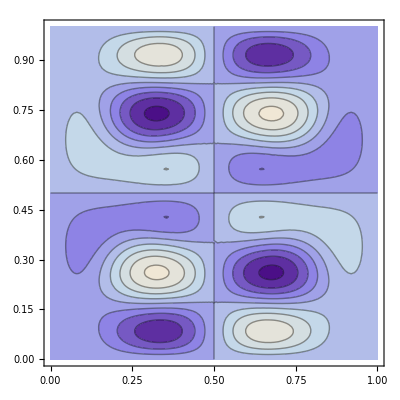

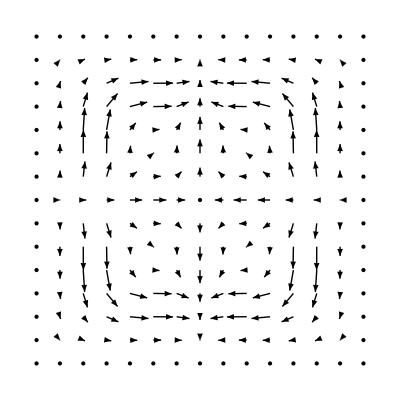

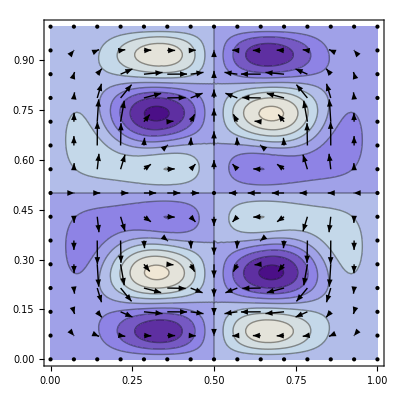

```mathematica
vorticity=ContourPlot[Evaluate[V[x,y,1.36/12 1/(4π),MixingAngle12,MixingAngle13,-1/4 1/(4π)]], {x, 0, 1}, {y, 0,1}]
flow=VectorFieldPlot[Evaluate[{JX[x,y,1.36/12 1/(4π),MixingAngle13,MixingAngle13,-1/4 1/(4π)],JY[x,y,1.36/12 1/(4π),MixingAngle13,MixingAngle13,-1/4 1/(4π)]}], {x, 0, 1}, {y, 0,1}]
Show[vorticity,flow]
```

we see little direct evidence that the two patterns are correlated. Evidentl the relationship between swirl and curl is a subtle one.

### Phase

Let  Ψ[x, y] be written in polar form:

```mathematica
Ψ[x,y]=R[x,y] ⅇ^(ⅈ S[x,y])
```

ⅇ^(ⅈ s[x,y,t][x,y]) r[x,y,t][x,y]

From

```mathematica
-ⅈ(R[x,y] ⅇ^(-ⅈ S[x,y])D[R[x,y] ⅇ^(+ⅈ S[x,y]),x]-R[x,y] ⅇ^(+ⅈ S[x,y])D[R[x,y] ⅇ^(-ⅈ S[x,y]),x])//Simplify
-ⅈ(R[x,y] ⅇ^(-ⅈ S[x,y])D[R[x,y] ⅇ^(+ⅈ S[x,y]),y]-R[x,y] ⅇ^(+ⅈ S[x,y])D[R[x,y] ⅇ^(-ⅈ S[x,y]),y])//Simplify
```

2 (r[x,y,t][x,y])^2 (s[x,y,t]^(1,0)[x,y]+s^(1,0,0)[x,y,t][x,y])

2 (r[x,y,t][x,y])^2 (s[x,y,t]^(0,1)[x,y]+s^(0,1,0)[x,y,t][x,y])

we see that the current vector has assumed the form

```mathematica
J[x,y]=2 P[x,y]({{Derivative[1,0][S]}, {Derivative[0,1][S]}})
```

{{2 (16/9 Sin[2 π x]^2 Sin[π y]^2+16/9 Sin[π x] Sin[2 π x] Sin[π y] Sin[2 π y]+20/9 Sin[π x]^2 Sin[2 π y]^2) s[x,y,t]^(1,0)},{2 (16/9 Sin[2 π x]^2 Sin[π y]^2+16/9 Sin[π x] Sin[2 π x] Sin[π y] Sin[2 π y]+20/9 Sin[π x]^2 Sin[2 π y]^2) s[x,y,t]^(0,1)}}

while from

```mathematica
D[2 R[x,y]^2 Derivative[0,1][S][x,y],x]-D[2 R[x,y]^2 Derivative[1,0][S][x,y],y]//Simplify
```

2 r[x,y,t][x,y] (-2 r[x,y,t]^(0,1)[x,y] s[x,y,t]^(1,0)[x,y]-2 s[x,y,t]^(1,0)[x,y] r^(0,1,0)[x,y,t][x,y]-r[x,y,t][x,y] (Derivative[1,0]'[s[x,y,t]] s^(0,1,0)[x,y,t])[x,y]+2 s[x,y,t]^(0,1)[x,y] (r[x,y,t]^(1,0)[x,y]+r^(1,0,0)[x,y,t][x,y])+r[x,y,t][x,y] (Derivative[0,1]'[s[x,y,t]] s^(1,0,0)[x,y,t])[x,y])

and

```mathematica
D[2 {P[x,y]/.P[x,y]->R[x,y]^2} ,x]
D[2 {P[x,y]/.P[x,y]->R[x,y]^2} ,y]
```

{4 r[x,y,t][x,y] (r[x,y,t]^(1,0)[x,y]+r^(1,0,0)[x,y,t][x,y])}

{4 r[x,y,t][x,y] (r[x,y,t]^(0,1)[x,y]+r^(0,1,0)[x,y,t][x,y])}

we see that the vorticity has assume the form

```mathematica
V[x,y]=2( P^(1,0)Derivative[0,1][S]-P^(0,1)Derivative[1,0][S])
```

as could, by the way, have been obtained directly from the identity

```mathematica
curl(scalar.vector)=scalar.curl(vector)+grad(scalar)×vector
```

grad scalar×vector+vector scalar.curl

What we have established is that current and its vorticity are both sensitive to the first derivatives of the phase, but insensitive to its absolute value.

Looking to the typical wave function

```mathematica
Ψ[x,y,t,MixingAngle12,MixingAngle13,-1/4 1/(4π)]//ComplexExpand
```

ⅈ Im[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,0.527788,1.31633,-1/(16 π)]]+Re[(4/3 ⅇ^(-5 ⅈ π^2 t) Sin[2 π x] Sin[π y]+(2/3+(4 ⅈ)/3) ⅇ^(-5 ⅈ π^2 t) Sin[π x] Sin[2 π y])[x,y,t,0.527788,1.31633,-1/(16 π)]]

we might extract the real/imaginary parts

```mathematica
re[x_,y_,t_]:=0.43494897097895274 Cos[π^2 t] Cos[π/16-π^2 t] Sin[π x] Sin[π y]+0.43494897097895274 Sin[π^2 t] Sin[π/16-π^2 t] Sin[π x] Sin[π y]+0.25355327515515014 Cos[9 π^2 t] Cos[π/16-π^2 t] Sin[3 π x] Sin[π y]+0.25355327515515014 Sin[9 π^2 t] Sin[π/16-π^2 t] Sin[3 π x] Sin[π y]+1.6722058977339354 Cos[π/16-9 π^2 t] Sin[π^2 t] Sin[π x] Sin[3 π y]-1.6722058977339354 Cos[π^2 t] Sin[π/16-9 π^2 t] Sin[π x] Sin[3 π y]+0.97481155352524 Cos[π/16-9 π^2 t] Sin[9 π^2 t] Sin[3 π x] Sin[3 π y]-0.97481155352524 Cos[9 π^2 t] Sin[π/16-9 π^2 t] Sin[3 π x] Sin[3 π y]
im[x_,y_,t_]:=-0.43494897097895274 Cos[π/16-π^2 t] Sin[π^2 t] Sin[π x] Sin[π y]+0.43494897097895274 Cos[π^2 t] Sin[π/16-π^2 t] Sin[π x] Sin[π y]-0.25355327515515014 Cos[π/16-π^2 t] Sin[9 π^2 t] Sin[3 π x] Sin[π y]+0.25355327515515014 Cos[9 π^2 t] Sin[π/16-π^2 t] Sin[3 π x] Sin[π y]+1.6722058977339354 Cos[π^2 t] Cos[π/16-9 π^2 t] Sin[π x] Sin[3 π y]+1.6722058977339354 Sin[π^2 t] Sin[π/16-9 π^2 t] Sin[π x] Sin[3 π y]+0.97481155352524 Cos[9 π^2 t] Cos[π/16-9 π^2 t] Sin[3 π x] Sin[3 π y]+0.97481155352524 Sin[9 π^2 t] Sin[π/16-9 π^2 t] Sin[3 π x] Sin[3 π y]
```

and proceed

```mathematica
Manipulate[Plot3D[Evaluate[ArcTan[im[x,y,n/12 1/(4π)]/re[x,y,n/12 1/(4π)]]], {x, 0, 1}, {y, 0,1}],{n,0,11}]
```

One gets much smoother results by using Mathematica's Arg command:

```mathematica
Manipulate[Plot3D[Evaluate[Arg[Ψ[x,y,n/12 1/(4π),MixingAngle12,MixingAngle13,-1/4 1/(4π)]]], {x, 0, 1}, {y, 0,1}],{n,0,11}]
```

The phase surface has resolved into sheets, with what appear to be 2π jumps at the cuts. Derivatives, on the other hand, appeaer to be continuous across the cuts.  The following figure displays the same information as a density plot:

-Graphics-

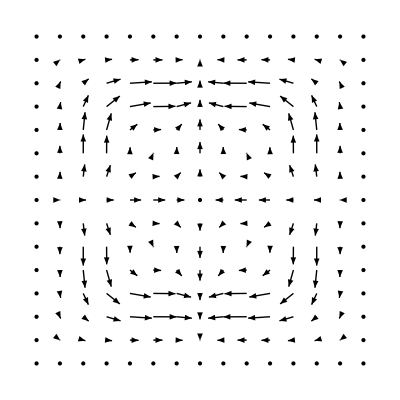

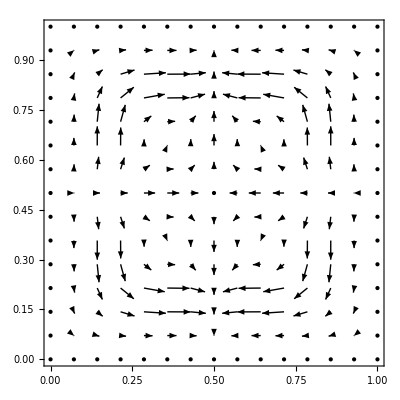

```mathematica
Phase=DensityPlot[Evaluate[Arg[Ψ[x,y,2.19/12 1/(4π),MixingAngle12,MixingAngle13,-1/4 1/(4π)]]], {x, 0, 1}, {y, 0,1}]
AssociatedFlow=VectorFieldPlot[Evaluate[{JX[x,y,2.19/12 1/(4π),MixingAngle13,MixingAngle13,-1/4 1/(4π)],JY[x,y,1.36/12 1/(4π),MixingAngle13,MixingAngle13,-1/4 1/(4π)]}], {x, 0, 1}, {y, 0,1}]
Show[Phase, AssociatedFlow]
```

we see that its value sometimes makes a 2π jump to another sheet, but that its derivatives appear to be join smoothly at the cuts.

### Concluding comments

```mathematica
Plot3D[Arg[x+ⅈ y], {x,-1,1},{y,-1,1}]
```

-Graphics3D-